#### Geometric wall model with a softened potential. Consult notes of ??

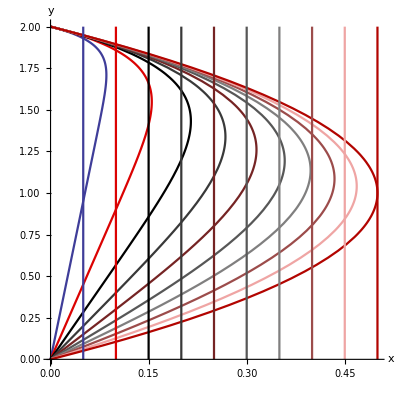

```mathematica
xsolδ=y0/(a/d-1)(y/y0-(y/y0)^(a/d));
δplts=Table[
ParametricPlot[
{xsolδ/.{a->1,y0->2,d->0.05*n},y},
{y,0,2},
PlotRange->{{0,Automatic},All},AxesLabel->{"x","y"},AspectRatio->1,PlotStyle->ColorData[n]],
{n,1,10}];
wplts=Table[
ParametricPlot[
{0.05*n,y},
{y,0,2},
PlotStyle->ColorData[n]],
{n,1,10}];
Show[
{δplts,wplts},
PlotRange->Automatic]
```

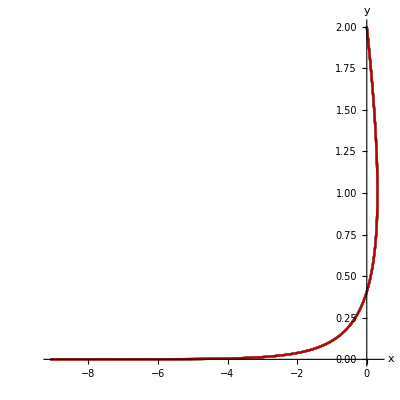

```mathematica
xsol=y0-y+a Log[y/y0];
plts=Table[
ParametricPlot[
{xsol/.{a->1,y0->2,d->0.05*n},y},
{y,0,2},
PlotRange->{{0,Automatic},All},AxesLabel->{"x","y"},AspectRatio->1,PlotStyle->ColorData[n]],
{n,1,10}];
Show[plts,
PlotRange->{{0,Automatic},All}]
```